```mathematica
rolls=RandomInteger[{1,10},{10,3}]
```

{{6,1,1},{3,5,10},{5,10,3},{5,7,3},{2,9,2},{4,3,2},{5,1,10},{7,7,5},{4,7,5},{7,7,6}}

Had some trouble figuring out how to use these numbers. I tried to Fold a function over each set of 3 numbers but every result was wrong. Mostly because I couldnt figure out how to access each element in the smaller set of 3 elements. Had trouble with most of this problem.

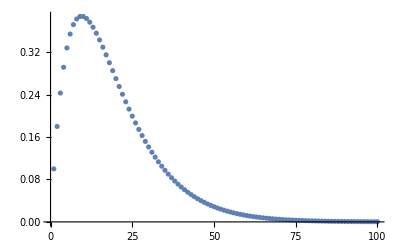

0.382638

0.38742

0.383546

```mathematica
func1[n_]:=n*Power[9,n-1]/Power[10,n];
ListPlot[List[func1[N[Range[100]]]]]
N[func1[8]]
N[func1[10]]
N[func1[11]]
```

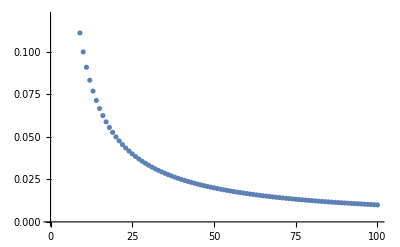

```mathematica
ListPlot[func[N[Range[1,100]]]]
```

```mathematica
expectedVal=N[Sum[x*Power[9,x-1]/Power[10,x],{x,1,Infinity}]]
```

10.